```mathematica
-Graphics-"16""♁""27""♁""35""♁""4"
```

```mathematica
g1=GraphFromSets[{{1,6},{2,7},{3,5},{4}}];
```

```mathematica
-Graphics-"13""♁""27""♁""4""♁""56"
```

```mathematica
g2=GraphFromSets[{{1,3},{2,7},{4},{5,6}}];
```

```mathematica
-Graphics-"14""♁""27""♁""3""♁""56",
```

```mathematica
g3=GraphFromSets[{{1,4},{2,7},{3},{5,6}}];
```

```mathematica
g4=GraphFromSets[{{1,4},{2,7},{3,5},{6}}]
```

{1<->2,1<->7,1<->3,1<->5,1<->6,4<->7,4<->5,4<->6,2<->4,2<->3,2<->5,2<->6,3<->4,3<->7,3<->6,5<->7,5<->6,6<->7}

```mathematica
Join[EdgeList[GraphComplement[g1]],EdgeList[GraphComplement[g2]],EdgeList[GraphComplement[g3]]]
```

{1<->6,2<->7,3<->5,1<->3,2<->7,5<->6,1<->4,2<->7,5<->6}

```mathematica
all12=EdgeDelete[CompleteGraph[7],DeleteDuplicates[Join[EdgeList[GraphComplement[g1]],EdgeList[GraphComplement[g2]]]]];
```

```mathematica
all23=EdgeDelete[CompleteGraph[7],DeleteDuplicates[Join[EdgeList[GraphComplement[g2]],EdgeList[GraphComplement[g3]]]]];
```

```mathematica
all13=EdgeDelete[CompleteGraph[7],DeleteDuplicates[Join[EdgeList[GraphComplement[g3]],EdgeList[GraphComplement[g1]]]]];
```

```mathematica
all=EdgeDelete[CompleteGraph[7],DeleteDuplicates[Join[EdgeList[GraphComplement[g1]],EdgeList[GraphComplement[g2]],EdgeList[GraphComplement[g3]]]]];
```

```mathematica
FindFullFormula[g1]
```

{v1x2x3x4x5x6x7,v1x2x35x4x6x7,v1x27x3x4x5x6,v1x27x35x4x6,v16x2x3x4x5x7,v16x2x35x4x7,v16x27x3x4x5,v16x27x35x4}

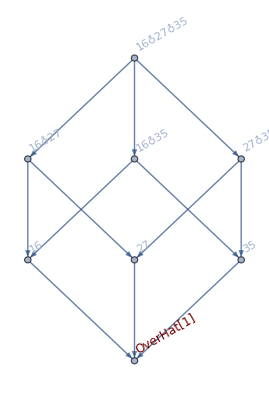

```mathematica
FindFullFormula[g1]//FormulaGraphReverse2
```

```mathematica
FindFullFormula[g2]
```

{v1x2x3x4x5x6x7,v1x2x3x4x56x7,v1x27x3x4x5x6,v1x27x3x4x56,v13x2x4x5x6x7,v13x2x4x56x7,v13x27x4x5x6,v13x27x4x56}

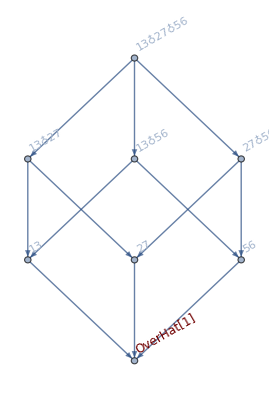

```mathematica
FindFullFormula[g2]//FormulaGraphReverse2
```

```mathematica
FindFullFormula[g3]
```

{v1x2x3x4x5x6x7,v1x2x3x4x56x7,v1x27x3x4x5x6,v1x27x3x4x56,v14x2x3x5x6x7,v14x2x3x56x7,v14x27x3x5x6,v14x27x3x56}

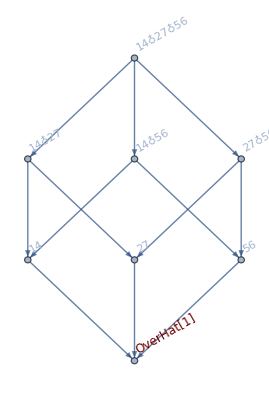

```mathematica
FindFullFormula[g3]//FormulaGraphReverse2
```

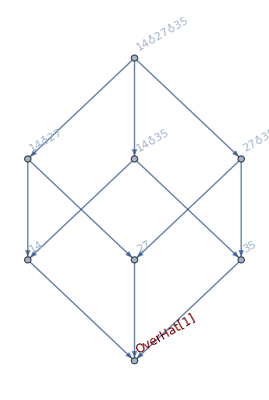

```mathematica
FindFullFormula[g4]//FormulaGraphReverse2
```

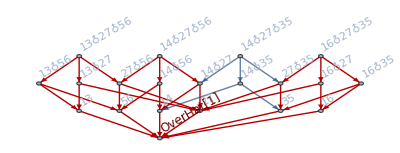

```mathematica
Graph[FormulaGraphReverse2[FindFullFormula[all]],GraphHighlight->EdgeList[GraphUnion[FormulaGraphReverse2[FindFullFormula[g1]],FormulaGraphReverse2[FindFullFormula[g2]],FormulaGraphReverse2[FindFullFormula[g3]]]]]
```

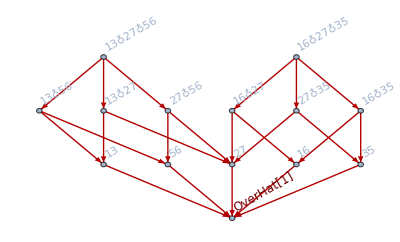

```mathematica
Graph[FormulaGraphReverse2[FindFullFormula[all12]],GraphHighlight->EdgeList[GraphUnion[FormulaGraphReverse2[FindFullFormula[g1]],FormulaGraphReverse2[FindFullFormula[g2]]]]]
```

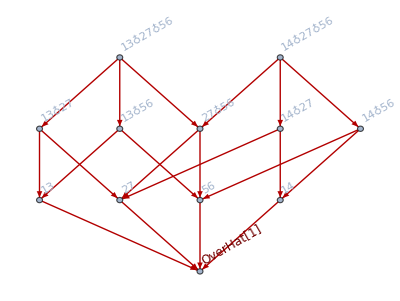

```mathematica
Graph[FormulaGraphReverse2[FindFullFormula[all23]],GraphHighlight->EdgeList[GraphUnion[FormulaGraphReverse2[FindFullFormula[g2]],FormulaGraphReverse2[FindFullFormula[g3]]]]]
```

```mathematica
ChromaticPolynomial[all13,4]
```

72

```mathematica
ChromaticPolynomial[g1,4]
```

24

```mathematica
ChromaticPolynomial[g3,4]
```

24

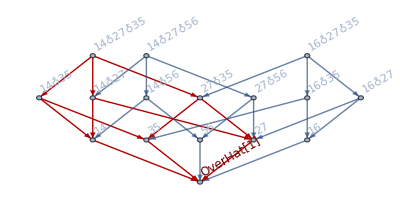

```mathematica
Graph[FormulaGraphReverse2[FindFullFormula[all13]],GraphHighlight->EdgeList[FormulaGraphReverse2[FindFullFormula[g4]]]]
```

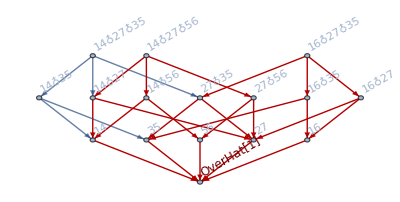

```mathematica
Graph[FormulaGraphReverse2[FindFullFormula[all13]],GraphHighlight->EdgeList[GraphUnion[FormulaGraphReverse2[FindFullFormula[g3]],FormulaGraphReverse2[FindFullFormula[g1]]]]]
```

```mathematica
Sum[Fold[Plus,FindFullFormula[g]],{g,{g1,g2,g3}}]
```

v13x27x4x56+v13x27x4x5x6+v13x2x4x56x7+v13x2x4x5x6x7+v14x27x3x56+v14x27x3x5x6+v14x2x3x56x7+v14x2x3x5x6x7+v16x27x35x4+v16x27x3x4x5+v16x2x35x4x7+v16x2x3x4x5x7+v1x27x35x4x6+2 v1x27x3x4x56+3 v1x27x3x4x5x6+v1x2x35x4x6x7+2 v1x2x3x4x56x7+3 v1x2x3x4x5x6x7

```mathematica
diff=Sum[Fold[Plus,FindFullFormula[g]],{g,{g1,g2,g3}}]-Fold[Plus,FindFullFormula[all]]
```

-v14x27x35x6-v14x2x35x6x7+v1x27x3x4x56+2 v1x27x3x4x5x6+v1x2x3x4x56x7+2 v1x2x3x4x5x6x7

```mathematica
FormulaGraphReverse2[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s1]->SetsToSymbol[s2]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[SymbolToLabel2[ SetsToSymbol[s]],Pi/6],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

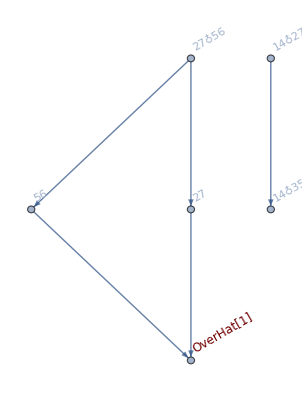

```mathematica
CompleteBaseCoeff[diff]//FormulaGraphReverse2
```